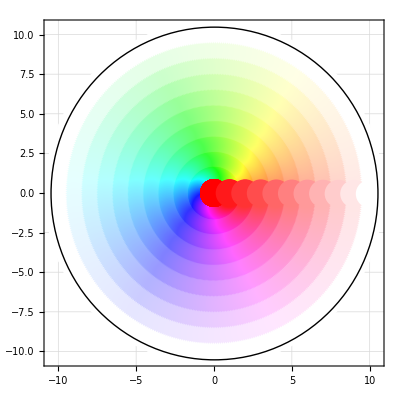

```mathematica
maxRadius = 10;

drawPoint[{angle_, radius_}] := {Hue[angle/(2*Pi), (1-radius/maxRadius), 1], Point[{radius*Cos[angle], radius*Sin[angle]}]}

Graphics[{PointSize[0.05], Table[drawPoint[{a, r}],{a, 0, 2*Pi, 5/360}, {r, 0, 10, 1}],Black,Circle[{0,0}, 10.5]}, Frame->True, GridLines->Automatic]
```